# PI

## Listas

Una dimensión

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
RandomInteger[10,20]
```

{0,4,2,3,8,1,4,1,1,10,2,2,3,8,0,0,1,7,8,3}

```mathematica
?Table
```

```mathematica
Table[42,7]
```

{42,42,42,42,42,42,42}

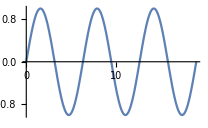

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
Table[-Graphics-,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[i+20,{i,1,10}]
```

{21,22,23,24,25,26,27,28,29,30}

```mathematica
Table[i+RandomInteger[100],{i,1,10}]
```

{93,52,82,46,66,57,90,27,91,69}

Longitud de una lista

```mathematica
Length[Range[15]]
```

15

Map

```mathematica
?Map
```

```mathematica
funcionCualquiera/@{1,2,3}
```

{funcionCualquiera[1],funcionCualquiera[2],funcionCualquiera[3]}

Dos dimensiones

```mathematica
lista=Table[{i,j},{i,4},{j,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}}}

```mathematica
lista⟦1⟧
```

{{1,1},{1,2},{1,3}}

```mathematica
Part[lista,1]
```

{{1,1},{1,2},{1,3}}

```mathematica
lista⟦1⟧==Part[lista,1]
```

True

```mathematica
Length[lista]
```

4

```mathematica
Length[lista⟦2⟧]
```

3

```mathematica
Length/@lista
```

{3,3,3,3}

### Ejercicio 1

Crear una lista de dos dimensiones. Que esté compuesta por 5 listas de 5 elementos cada una.

Forma 1

```mathematica
Table[Table["a",5],5]
```

{{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a}}

```mathematica
Length[Table[Table["a",5],5]]
```

5

```mathematica
Length/@Table[Table["a",5],5]
```

{5,5,5,5,5}

Forma 2

```mathematica
Table["a",5,5]
```

{{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a}}

Forma 3

```mathematica
ConstantArray["a",{5,5}]
```

{{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a},{a,a,a,a,a}}

### Ejercicio 2

Crear una lista de dos dimensiones. Que esté compuesta por 20 listas de 10 elementos cada una.

```mathematica
ConstantArray["a",{20,10}]
```

{{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a},{a,a,a,a,a,a,a,a,a,a}}

```mathematica
ConstantArray["a",{20,10}]//MatrixForm
```

(a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a
a | a | a | a | a | a | a | a | a | a)

### Ejercicio 3

Crear una lista de dos dimensiones. Que esté compuesta por 20 listas de 10 elementos cada una y cada elemento tiene que ser un número entero aleatorio entre 0 y 100.

```mathematica
?RandomInteger
```

```mathematica
RandomInteger[20]
```

17

```mathematica
ConstantArray[RandomInteger[100],{20,10}]//MatrixForm
```

(68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68
68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68 | 68)

```mathematica
Table[RandomInteger[100],20,10]//MatrixForm
```

(34 | 66 | 27 | 70 | 71 | 48 | 20 | 79 | 63 | 41
9 | 34 | 16 | 17 | 89 | 79 | 75 | 94 | 41 | 33
51 | 82 | 31 | 40 | 29 | 51 | 67 | 35 | 83 | 49
76 | 7 | 24 | 76 | 59 | 93 | 63 | 94 | 75 | 98
29 | 29 | 69 | 11 | 38 | 13 | 24 | 98 | 53 | 74
57 | 65 | 58 | 28 | 93 | 31 | 22 | 86 | 13 | 100
64 | 58 | 69 | 37 | 79 | 91 | 26 | 83 | 58 | 10
2 | 9 | 75 | 27 | 45 | 5 | 63 | 27 | 83 | 7
77 | 21 | 79 | 50 | 41 | 89 | 61 | 49 | 50 | 65
32 | 84 | 68 | 33 | 17 | 41 | 89 | 96 | 94 | 23
29 | 34 | 27 | 47 | 22 | 93 | 63 | 44 | 15 | 67
45 | 49 | 31 | 97 | 3 | 89 | 34 | 3 | 56 | 11
84 | 30 | 68 | 5 | 55 | 41 | 99 | 68 | 84 | 52
28 | 28 | 60 | 2 | 22 | 17 | 80 | 99 | 22 | 24
3 | 9 | 73 | 85 | 91 | 7 | 89 | 21 | 16 | 39
100 | 54 | 77 | 76 | 32 | 69 | 69 | 17 | 69 | 77
19 | 87 | 37 | 11 | 65 | 98 | 69 | 37 | 62 | 76
18 | 91 | 60 | 28 | 57 | 46 | 72 | 91 | 39 | 55
87 | 46 | 57 | 25 | 8 | 28 | 18 | 76 | 40 | 57
68 | 76 | 94 | 73 | 97 | 36 | 45 | 68 | 94 | 7)

## Imágenes

### Image

Crear una imagen

```mathematica
?Image
```

```mathematica
Image[Table[0,10,15]]
```

-Graphics-

```mathematica
Image[Table[RandomReal[],10,15]]
```

-Graphics-

```mathematica
Head[-Graphics-]
```

Image

Tarea: Utilizar Image con colores RGB (ver documentación de Image)

### Import

Importar imágenes desde internet

```mathematica
?Import
```

```mathematica
imagen=Import["https://public-media.si-cdn.com/filer/cc/bb/ccbb5e39-e6f0-4d6e-9b64-c1ae44b58f5c/istock-611295678.jpg"]
```

-Graphics-

### Dimensiones (tamaño)

```mathematica
ImageDimensions[imagen]
```

{2309,1299}

### Cambiar dimensiones

```mathematica
imagen=ImageResize[imagen,{800,600}]
```

-Graphics-

### Particionar imagen

```mathematica
?ImagePartition
```

```mathematica
imagenGrid=ImagePartition[imagen,60]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ImagePartition[imagen,60]//Length
```

10

```mathematica
Length/@ImagePartition[imagen,60]
```

{13,13,13,13,13,13,13,13,13,13}

Con esto concluímos que la imagen ha sido particionado en 10 filas y 13 columnas.

### Creando matriz

```mathematica
Image[ConstantArray[0,{60,60}]]
```

-Graphics-

```mathematica
blackGrid=ConstantArray[Image[ConstantArray[0,{60,60}]],{10,13}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Image[ConstantArray[0,{60,60}]]//ImageDimensions
```

{60,60}

```mathematica
ImageDimensions[-Graphics-]
```

{60,60}

### Intercambiar elementos

```mathematica
imagenGrid⟦3⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
imagenGrid⟦3,6⟧
```

-Graphics-

```mathematica
blackGrid⟦3,6⟧
```

-Graphics-

```mathematica
?ReplacePart
```

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
ReplacePart[Range[10,20],5-> "foo"]
```

{10,11,12,13,foo,15,16,17,18,19,20}

```mathematica
ReplacePart[Range[10,20],{5-> "foo",8-> "bar"}]
```

{10,11,12,13,foo,15,16,bar,18,19,20}

```mathematica
ImageAssemble[ReplacePart[blackGrid,{3,6}-> imagenGrid⟦3,6⟧]]
```

-Graphics-

```mathematica
ImageAssemble[ReplacePart[blackGrid,{{3,6}-> imagenGrid⟦3,6⟧,{7,7}-> imagenGrid⟦7,7⟧}]]
```

-Graphics-

Voy a crear una función que me permita reemplazar cuadrados negros por partes de la imagen original

```mathematica
encenderImagen[gridBase_,gridImagen_,pos_]:=ReplacePart[gridBase,pos-> gridImagen⟦pos⟦1⟧,pos⟦2⟧⟧]
```

```mathematica
encenderImagen[blackGrid,imagenGrid,{3,5}]
```

```mathematica
ImageAssemble[encenderImagen[blackGrid,imagenGrid,{RandomInteger[{1,10}],RandomInteger[{1,13}]}]]
```

-Graphics-

```mathematica
Manipulate[ImageAssemble[encenderImagen[blackGrid,imagenGrid,{i,5}]],{i,1,10,1}]
```

### Creando una animación

```mathematica
ListAnimate[Table[ImageAssemble[encenderImagen[blackGrid,imagenGrid,{RandomInteger[{1,10}],RandomInteger[{1,13}]}]],20]]
```

## Tarea

Extender la función encenderImage para que pueda encender más de un cuadrado a la vez

Map

Probar con más imágenes

## Apéndice 1: Diferentes formas de aplicar una función

```mathematica
FullForm[Range[10]]
```

List[1,2,3,4,5,6,7,8,9,10]

```mathematica
FullForm@Range[10]
```

List[1,2,3,4,5,6,7,8,9,10]

```mathematica
Range[10]//FullForm
```

List[1,2,3,4,5,6,7,8,9,10]

```mathematica
Head[Range[10]]
```

List

```mathematica
Range[10]⟦0⟧
```

List

```mathematica
Head["Una cadena de caracteres"]
```

String